## CA Manipulation

```mathematica
initialValues=SparseArray[{{10,11}->1,{11,10}->1,{11,11}->1,{11,12}->1,{12,11}->1},{21,21}]; (* Define starting values and lattice size. *)
```

```mathematica
cellState[cell_,lattice_]:=lattice[[cell[[1]],cell[[2]]]]; (* Returns the value of the cell {x,y}. *)
```

```mathematica
Options[vonNeumannNeighborhood]={"CellShape"->Square};

vonNeumannNeighborhood[cell_,lattice_,OptionsPattern[vonNeumannNeighborhood]]:=
Module[
	{c1=cell[[1]],c2=cell[[2]],s=OptionValue["CellShape"]},
	Which[
		s===Square,
			{c1,c2}->{{c1-1,c2},{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2}},
			
		s===Hexagon,
			{c1,c2}->{{},{},{c1,c2-1},{c1,c2},{c1,c2+1},{},{}},
			
		s===Triangle,
			If[EvenQ[c2],
				{c1,c2}->{{c1,c2-1},{c1,c2},{c1,c2+1},{c1+1,c2-1}},
				{c1,c2}->{{c1-1,c2+1},{c1,c2-1},{c1,c2},{c1,c2+1}}
				]
			]
]; (* Associates the cell to its von Neumann Neighborhood. *)
```

```mathematica
vonNeumannNeighborhood[{10,10},initialValues,"CellShape"->Square]
```

{10,10}→{{9,10},{10,9},{10,10},{10,11},{11,10}}

```mathematica
Options[vNNTable]:={"CellShape"->Square};

vNNTable[lattice_,OptionsPattern[vNNTable]]:=
Association[
	Flatten[
		Table[
			vonNeumannNeighborhood[
				{i,j},lattice,"CellShape"->OptionValue["CellShape"]
			],
			{i,1,Dimensions[lattice][[1]]},{j,1,Dimensions[lattice][[2]]}
		],1
	]
]; (* Associates all cells to their  von Neumann neighborhoods. *)
```

```mathematica
vonNeumannNeighborhoods=vNNTable[initialValues,"CellShape"->Square]
```

<|{1,1}→{{0,1},{1,0},{1,1},{1,2},{2,1}},{1,2}→{{0,2},{1,1},{1,2},{1,3},{2,2}},{1,3}→{{0,3},{1,2},{1,3},{1,4},{2,3}},{1,4}→{{0,4},{1,3},{1,4},{1,5},{2,4}},{1,5}→{{0,5},{1,4},{1,5},{1,6},{2,5}},432,{21,18}→{{20,18},{21,17},{21,18},{21,19},{22,18}},{21,19}→{{20,19},{21,18},{21,19},{21,20},{22,19}},{21,20}→{{20,20},{21,19},{21,20},{21,21},{22,20}},{21,21}→{{20,21},{21,20},{21,21},{21,22},{22,21}}|>
 |  |  |  |

```mathematica
neighborhoodState[cell_,globalState_]:=
Quiet[
	Module[
		{n=vonNeumannNeighborhoods[[Key[cell]]]},
		Table[
			If[IntegerQ[cellState[n[[i]],globalState]],
				cellState[n[[i]],globalState],
				0
			],
		{i,1,Length[n]}
		]
	]
]; (* Returns the state of each cell in the von Neumann neighborhood of the specified cell. *)
```

```mathematica
rules=<|{0,0}->0,{0,1}->1,{0,2}->0,{0,3}->1,{0,4}->0,{1,1}->0,{1,2}->1,{1,3}->0,{1,4}->1,{1,5}->0|>; (* An example set of rules. *)
```

```mathematica
cellEvolution[cell_,globalState_,rule_]:=
Lookup[
	rule,{{cellState[cell,globalState],Total[neighborhoodState[cell,globalState]]}}][[1]];(* Applies the specified evolution rule to the particular cell. *)
```

```mathematica
globalEvolution[state_,func_Function]:=
Module[
	{rules},
	rules=AssociationMap[
					func@@#&,
					Flatten[
						Table[
							{i-1,j-1},
							{i,1,2},
							{j,1,8}
							],
						1
					]
			];
	SparseArray[{i_,j_}:>cellEvolution[{i,j},state,rules],Dimensions[state]]
]; (* Applies the specified rule to the current state. *)
```

## CA Graphics

#### 2D Graphics

```mathematica
Options[LatticePlot]:={"CellShape"->Square};

LatticePlot[lattice_,basis_List:{{1,0},{0,1}},OptionsPattern[LatticePlot]]:=
Graphics[
	Module[
		{b1=basis[[1]],b2={-basis[[2,1]],basis[[2,2]]},d1=Dimensions[lattice][[1]],d2=Dimensions[lattice][[2]],s=OptionValue["CellShape"]},
		Which[
			s===Square,
				Table[
					{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
					EdgeForm[Black],
					Polygon[{b1*j-b2*i,b1*(j+1)-b2*i,b1*(j+1)-b2*(i+1),b1*j-b2*(i+1)}]},
				{i,1,d1},{j,1,d2}],
				
			s===Hexagon,
				Message["Not implemented yet..."],
				
			s===Triangle,
				Table[
					If[OddQ[j],
					
						{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
						EdgeForm[Black],
						Triangle[{b1*((j-1)/2)-b2*(i-1),b1*((j+1)/2)-b2*(i-1),b1*(j-1)/2-b2*(i)}]},
						
						{FaceForm[GrayLevel[1-cellState[{i,j},lattice]]],
						EdgeForm[Black],
						Triangle[{b1*(j/2)-b2*(i-1),b1*(j/2-1)-b2*(i),b1*(j/2)-b2*(i)}]}],
				{i,1,d1},{j,1,d2}]
		]
	],
	ImageSize->300
]; (* Plots the triangular lattice with given state. *)
```

```mathematica
Options[CAPlot]:={"CellShape"->Square};

CAPlot[lattice_,func_Function,time_Integer,basis_List:{{1,0},{0,1}},OptionsPattern[CAPlot]]:=
Module[
	{vNN=vNNTable[lattice,"CellShape"->OptionValue["CellShape"]],timestate=Nest[globalEvolution[#,func]&,lattice,time]},
	Graphics[
		LatticePlot[
			timestate,
			basis,
			"CellShape"->OptionValue["CellShape"]
		]
	]
]; (* Plots the CA after applying the rule "func" to the initial lattice "times" times. *)
```

```mathematica
Options[CAEvolution]:={"CellShape"->Square};

CAEvolution[lattice_,func_Function,time_Integer,basis_List:{{1,0},{0,1}},OptionsPattern[CAEvolution]]:=
Module[
	{vNN=vNNTable[lattice,"CellShape"->OptionValue["CellShape"]],timestate=NestList[globalEvolution[#,func]&,lattice,time]},
	Animate[
		Graphics[
			LatticePlot[
				timestate[[n]],
				basis,
				"CellShape"->OptionValue["CellShape"]
			]
		],
	{{n,1},1,time,1},
	AnimationRate->2,
	AnimationRunning->False
	]
]; (* Animates the evolution of a CA. *)
```

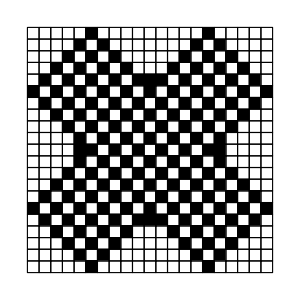

```mathematica
Row[{CAPlot[initialValues,Mod[#1+#2,2]&,15,"CellShape"->Square],CAEvolution[initialValues,Mod[#1+#2,2]&,30,"CellShape"->Square]}]
```

#### 1D Graphics

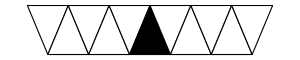

```mathematica
initialValues1D=SparseArray[{{1,6}->1},{1,11}];
basis1D={{1,0},{0.5,Sqrt[3]/2}};
LatticePlot[initialValues1D,basis1D,"CellShape"->Triangle]
```

```mathematica
CAEvolution[initialValues1D,Mod[#1+#2,2]&,10,{{1,0},{0.5,Sqrt[3]/2}},"CellShape"->Triangle]
```